# MMA 语法

## 1. 自定义函数

1. 简单的函数：模式匹配 + 延迟赋值
例如”f[x_]:=2x-1”定义了数学函数f(x)=2x-1。其中”x_”称为模式。这是一类重要实体，它可以表示函数定义中的变量，可以看成高级语言函数定义的形式参数。模式”x_”表示匹配任何形式参数的表达式。”x_”可为实数、向量或矩阵
f[x_]:=x^2;
f[x_,y_]:=x+y; 

2. 纯函数(和C语言十分类似):λ-表达式， 匿名函数(建议初学者使用此种方法)，如
f = Function[x,x^2]; ↔ f = #^2 &;(*对应的简写形式*)
g = Function[{x, y}, x*y]  ↔  g=#1*#2 &;(*对应的简写形式*)

不带模式匹配

g1[2]

g1[{1,2,3}]

带有模式匹配

2

{3,4,5}

{0,0,0}

4/π^2+2/π

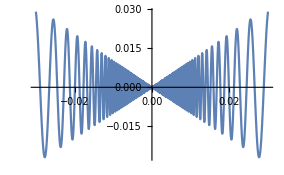

```mathematica
ls5 = {1, 2, 3};
ls6 ={-1, -2, -3};
(*1. 不带模式匹配*)
Print["不带模式匹配"];
g1[x]=2x;
g1[2]
g1[ls5]

(*2. 带有模式匹配*)
Print["带有模式匹配"];
g2[x_, y_]:=x+y;
g2[1,1]
g2[ls5, 2]
g2[ls5, ls6]

(*3.绘制一个函数:格式必须正确*)
g3[x_]:=x Sin[1/x]+x^2;
g3[2/π]
Plot[g3[x],{x, -0.03, 0.03}]
```

反思

说明：f[x_]:=2x-1中的x同数学函数f(x)中的x的功能基本相同，都起着自变量的作用.
1. 在Mathematica中将x_称为规则变量或模式变量。
2. 而f[x]中的x类似于数学里的一个常量。
3. 即f[x]只代表f[x_]在某一点的值。

## 二：Wolfram编程

## Mathematica中的数据类型（Atom类型）：基本类型和构造类型 基本数据类型：整数，有理数，实数，复数 构造数据类型：表 Mathematica 内部定义的常数（LaTeX中使用Times New Roman字体效果更好。对比两种字体： 和 α + β = γ） Piπ Eⅇ Degree 角度到弧度的转换 π/180 I虚数 ⅈ,√-1 EulerGamma 欧拉常数 γ 0.577721 Infinity ∞

## 1. 变量

### 1.1 变量的命名

-Graphics-

```mathematica
(*1. 希腊字母测试*)
α=1;
α

(*2. 中文测试*)
变量 = 2;
变量


(*3. 下标*)
Subscript[S, 1]=3;
Subscript[S, 1]

(*4.Tips*)
(*变量中不能用下划线_*)
(*str_2 = "Hello";
str_2*)
str2 = "Hello";
str2
(*注：Head函数可以判断类型*)
Head[str2]
```

1

2

3

Hello

String

### 1.2 变量的赋值和使用

Mathematica为变量赋值提供了“=”与“:”两个运算符，这两个运算符也称为赋值运算符，其中前一个运算符为“立即赋值”运算符，后一个运算符为“延迟赋值”运算符。
立即赋值: 指的是赋值符“=”右侧的表达式立即被求值
延时赋值: 指的是赋值运算符“:”右侧表达式在定义时不求值，只是在调用该语句时才进行求值。

```mathematica
x = 1; y=2;
(*1. 运行之后会出现： 3*)
a = x+y

(*2. 运行之后什么也不出现*)
b := y+x
```

3

3

15

{1,2,3}

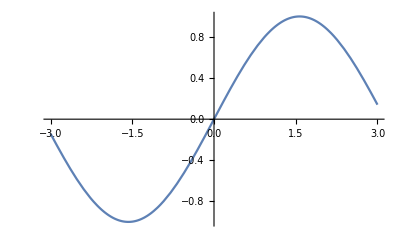

```mathematica
x=3(*给变量x赋值*)
y=x^2+2*x(*体将一多项式赋给变量y*)
z = {1,2,3}(*将一数组赋给变量z*)
f=Plot[Sin[x],{x,-3,3}];(*将一图像赋给变量*)
Show[f]
```

### 1.3 变量的消除

-Graphics-

```mathematica
(*注：没有赋值为蓝色，赋值后为黑色*)

(*方法一：使用Clear[]*)
x = 1;
x
Clear[x](*清除变量x的值也可以使用语句：Clear["x"]*)
x

(*方法二：赋为空值*)
x = 2;
x
x=.(*尝试清除变量x的值*)
x

(*方法三：退出内核；因为Mathematica默认分为前端和内核*)
(*-Graphics-，可以清空全部变量*)

(* 方法四：清除全部变量 *)
(*Clear["Global`"]*)
```

1

x

2

x

```mathematica
x=2
```

2

```mathematica
x
```

2

### 1.4 变量替换

```mathematica
(*原来的式子*)
z = x1+y1;
z

(*方法一:/.*)
res1 = z/.{x1->t11, y1->t21};
res1

(*方法二：ReplaceAll[];不是Replace[]*)
res2 = ReplaceAll[z, {x1->t12, y1->t22}];
res2
```

x1+y1

t11+t21

t12+t22

### 1.5 字符串

```mathematica
str1 = "abcdef"
str2 = "a\\b\tc\\d\te\\f\n第二行\t  α+β=γ"(*空格也是有效的*)
```

abcdef

a\b	c\d	e\f
第二行	  α+β=γ

```mathematica
(*字符串的处理函数*)

(*1. 分拆*)
ls1 = Characters["Hello"];
ls1

(*2. 组合*)
ls2 = StringJoin["Hello"," ","World"];
ls2

(*3.求长度*)
ls3 = StringLength["Hello "];
ls3

(*4.分割*)
ls4 = StringSplit["He#ll#o","#"];
ls4

(*5.转为表达式，类似的就还有一个ToString[]*)
fun = "x+y";
ls5 = ToExpression[fun];
fun/.{x->1,y->2}(*此时的fun仍然时字符变量无法求值*)
ls5/.{x->1,y->2}(*此时的ls5已经是符号表达式了，可以替换求值*)
(*Head函数可以判断类型*)
Head[ls5]
```

{H,e,l,l,o}

Hello World

6

{He,ll,o}

x+y

3

Plus

-Graphics-

### 1.6 ToString 命令

1. 可以和 StringJoin 命令配合
2. 把一个 matlab 中的列表转化为 MMA 中的列表

ls = "[[1, 2], [3, 4], [5, 6]]";
ls /. ['[']

```mathematica
"π Square Is: "<>ToString[N[Pi^2]]
```

π Square Is: 9.8696

```mathematica
StringJoin["π Square Is: ", ToString[N[Pi^2]]]
```

π Square Is: 9.8696

### 1.7 字符串替换功能

```mathematica
StringReplace["abbaabbaa", "ab"->"X"]
```

XbaXbaa

常见的 Matlab 矩阵变量转为MMA格式矩阵变量

```mathematica
var = StringReplace["[[1, 2]]",{"["->"{", "]"->"}"}]//List
```

{{{1, 2}}}

```mathematica
Flatten[%, 1]
var[[1]]//Head
```

{{{1, 2}}}

String

## 2.Mathematica中的表达式

Mathematica中的所有对象都可以被认为是表达式，Mathematica的运算过程就是表达式的求值过程
1. 基本表达式单元：常量，变量
2. 复合表达式：通过函数或者是运算符连接起来的多个基本表达式

2.1 常见的算术运算符（和C语言相同）

```mathematica
(*使用样例*)
num = 1;

(*1. 自增：和C语言相同*)
num++
++num
num

(*2. 符合运算符:+=,/=*)
num2 = 3;
num2 += 1;
num2
num2 /= 2;
num2
```

1

3

3

4

2

### 2.2 常见的关系运算符（和C语言相同）

-Graphics-

### 2.3 常见的逻辑运算符（相比C多了对应的And, Or, Not,Xor; 增加了Implies）

-Graphics-

```mathematica
Clear[m];
res3 =And[m>1, m<2]
m = 1.1;
res3
```

m>1&&m<2

True

## 2. 列表

类似于Python的列表推导式

### 2.1 生成列表

```mathematica
ls=Table[i^2, {i, 1, 10}]
ls2 = Table[{i, 2i}, {i, 1, 10, 2}]
```

{1,4,9,16,25,36,49,64,81,100}

{{1,2},{3,6},{5,10},{7,14},{9,18}}

### 2.2 列表标记

```mathematica
Table[Labeled[nodes[[i]],nets[[i]]], {i, 9}]
```

Part::partd: 部分指定 nodes⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 nets⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 nodes⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

{nodes⟦1⟧nets⟦1⟧,nodes⟦2⟧nets⟦2⟧,nodes⟦3⟧nets⟦3⟧,nodes⟦4⟧nets⟦4⟧,nodes⟦5⟧nets⟦5⟧,nodes⟦6⟧nets⟦6⟧,nodes⟦7⟧nets⟦7⟧,nodes⟦8⟧nets⟦8⟧,nodes⟦9⟧nets⟦9⟧}

```mathematica
Labeled[#,#]&/@Table[Prime[n],{n,10}]
```

{22,33,55,77,1111,1313,1717,1919,2323,2929}

## 三：流程控制

## 1. 简单条件判断

```mathematica
(*1. 一个分支*)
If[True,Print["为真"]]

(*2. 两个分支*)
If[False,Print["为真"],Print["为假"]]

(*3. default参数的使用*)
If[a==b,Print["为真"],Print["为假"], Print["无法判断"]]
```

为真

为假

为真

为假

无法判断

无法判断

## 2. 多重条件的判断

```mathematica
(*与C语言不同的是，在Mathemtica中使用逗号(,)表示一个语句，而前者使用分号(;)
for(i=0,j=1;    i<1;   i++)

For[i=0;j=1,    i<1,   i++]
*)
x = 1;
(*x=4;*)
Which[x==1,Print["x的值=1"], 
	x==2,Print["x的值=2"], 
	x==3,Print["x的值=3"], 
	True, Print["x的值不等于1, 2, 3"]
]
```

x的值=1

## 3. 循环

注意：在Mathematica中其实条件和循环用的并不多，原因如下
条件结构：几乎都可以通过核心语言中的匹配模式来完成。
循环结构：可以通过表处理和泛函编程来完成
提供的循环有:Do[], While[], For[];其中Do[]最简单

```mathematica
(*1. Do[]循环*)
Do[Print["Hello"], 3]
Do[Print[i], {i,2, 3}]
(*注：这条语句和上面的语句等价
Do[Print[i],{i, {1, 2, 3, 4} }]
*)


(*2. For[]循环:一个阶乘函数*)
For[i=2; t=i, i<4, i++, Print[t*=i]]
(*注：不推荐使用 Break,Continue, Goto等语句*)

(*3. While[]循环*)
n = 5; n=5; While[EvenQ[n--]]
```

Hello

Hello

Hello

2

3

4

12